```mathematica
c=2.9979*^8;
ℏ=1.05*^-34;
k=1.3806*^-23;

γ[side_]:=Block[{},
Switch[side,
1,4.521*^13,
2,0,
_,0
]
]
ωp[side_]:=Block[{},
Switch[side,
1,1.37*^16,
2,8.85938*^15,
_,0
]
]
ϵinf[side_]:=Block[{},
Switch[side,
1,1,
2,1.035,
_,0
]
]
ϵ0[side_]:=Block[{},
Switch[side,
1,0,
2,11.87,
_,0
]
]

ϵi[ω_, model_, side_]:=Block[{},
Switch[model,
1,1+(ωp[side]/ω)^2,
2,Switch[side,
1,1+ωp[side]^2/(ω(ω+γ[side])), (* Drude Model *)
2,ϵinf[side]+(ϵ0[side]-ϵinf[side])/(1-(ω/ωp[side])^2) (* Dielectric Model *),
_,0
],
_,0
]
]

r[ω_,κ_,pol_,model_,side_]:=Block[{ϵr,l,r},
ϵr=ϵi[ω,model,side];
l=Sqrt[ω^2*(ϵr-1)+c^2κ];
r=Switch[pol,
1,c κ,
2,c κ*ϵr
];
Return[(l-r)/(l+r)]
]
rsquared[ω_,κ_,pol_,model_]:=r[ω,κ,pol,model,1]*r[ω,κ,pol,model,2]

ωIntegral[κ_,model_,L_]:=Block[{},
integ[lim_?NumberQ]:=NIntegrate[(Log[1-rsquared[ω,κ,1,model]*Exp[-2*κ*L]]+Log[1-rsquared[ω,κ,2,model]*Exp[-2*κ*L]]),{ω,0,lim},AccuracyGoal->3];
integ[c*κ]
]

ηE[model_,L_]:=Block[{},
-((180.0*L^3)/(c*Pi^4))NIntegrate[κ*ωIntegral[κ,model,L],{κ,10.^-1,1.6*^7},AccuracyGoal->3]
]
```

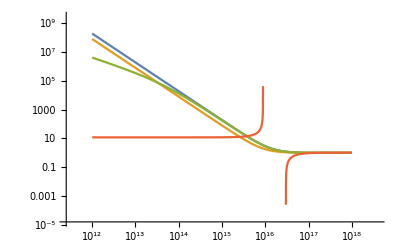

```mathematica
(* Plot Conductivity Models *)
ϵs=Flatten[Table[ϵi[ω,i,j],{i,1,2},{j,1,2}]];
LogLogPlot[ϵs,{ω,10^12,10^18}]
```

```mathematica
ηplasma=Table[{10.0^exp,ηE[1,10.0^(exp)]},{exp,-7,-4,0.1}];
```

```mathematica
ηdrude=Table[{10.0^exp,ηE[2,10.0^(exp)]},{exp,-7,-4,0.1}];
```

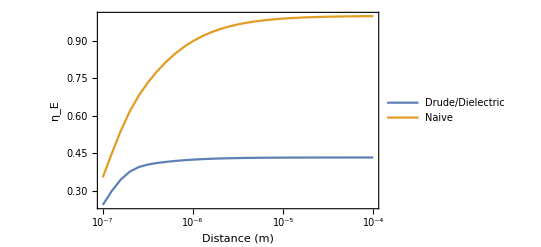

```mathematica
ListLogLinearPlot[{ηdrude,ηplasma},Frame->True,PlotRangePadding->{None,0.1},FrameLabel->{"Distance (m)","η_E"},ImageSize->Scaled[0.8],Joined->True,PlotLegends->{"Drude/Dielectric","Naive"}]
```

```mathematica
Eperfect[L_,R_]:=Block[{},
-(Pi^3ℏ c/720.)(R/(L^2))(1.+0.3333333(L/R))
]

Fperfect[L_,R_]:=Block[{},
(2ℏ c Pi^3/720)*(R/(L^3))*(1+0.3333333*L/R)
]

ηplasmaInterp=Interpolation[ηplasma];
ηdrudeInterp=Interpolation[ηdrude];
ηInterp[model_,L_]:=Block[{},
Switch[model,
1,ηplasmaInterp[L],
2,ηdrudeInterp[L],
_,0
]
]

ψ[L_,r_,R_]:=R (1-Sqrt[1-r^2/R^2])+L
dψsq[r_,R_]:=1/((R^2/r^2)-1)
Integrand[model_,L_,r_,R_]:=Block[{},
(ηInterp[model,ψ[L,r,R]]/(ψ[L,r,R]^3))(1+(1/3)dψsq[r,R])
]
Integrand0[model_,L_,r_,R_]:=Block[{},
(1/(ψ[L,r,R]^3))(1+(1/3)dψsq[r,R])
]

Ec[model_,L_,R_]:=Block[{},
intval[Lval_?NumericQ]:=NIntegrate[Integrand[model,Lval,r,R],{r,0.0,0.5R},AccuracyGoal->2];
-(2Pi^3 ℏ c/720.)*intval[L]
]

Fc[model_,L_,R_]:=Block[{},
Limit[(Ec[model,L+x,R]-Ec[model,L,R])/x,x->0]
]

f[T_,L_]:=Block[{ξ},
ξ=k*T*L/(ℏ c);
If[ξ≤ 0.5,
(ξ^3/(2Pi))*1.202-(ξ^4Pi^2/45),(ξ/(8Pi))*1.202-(Pi^2/720)
]
]
TempCorrection[T_,L_]:=Block[{},
1.+(720./Pi^2)*f[T,L]
]

Fcorrected[model_,L_,R_,T_]:=Block[{},
ηInterp[model,L]*Fperfect[L,R]*TempCorrection[T,L]
]
Ecorrected[model_,L_,R_,T_]:=Block[{},
ηInterp[model,L]*Eperfect[L,R]*TempCorrection[T,L]
]
```

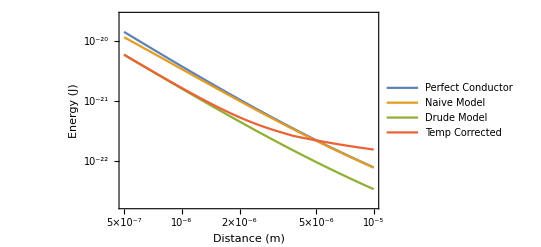

```mathematica
radius=2.5*^-6;
LogLogPlot[{-Eperfect[L,radius],-Ecorrected[1,L,radius,0],-Ecorrected[2,L,radius,0],-Ecorrected[2,L,radius,300]},{L,5.*^-7,1*^-5},Frame->True,PlotRangePadding->{None,0.1},PlotRange->{{5.*^-7,1*^-5},Full},FrameLabel->{"Distance (m)","Energy (J)"},ImageSize->Scaled[0.8],PlotLegends->{"Perfect Conductor","Naive Model","Drude Model","Temp Corrected"}]
```

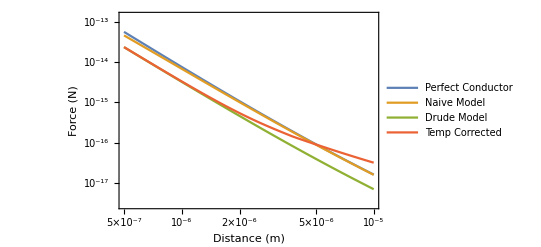

```mathematica
LogLogPlot[{Fperfect[L,radius],Fcorrected[1,L,radius,0],Fcorrected[2,L,radius,0],Fcorrected[2,L,radius,300]},{L,5.0*^-7,1*^-5},Frame->True,PlotRangePadding->{None,0.1},PlotRange->{{5.*^-7,1*^-5},Full},FrameLabel->{"Distance (m)","Force (N)"},ImageSize->Scaled[0.8],PlotLegends->{"Perfect Conductor","Naive Model","Drude Model","Temp Corrected"}]
```

```mathematica
Larray={1*^-5,5*^-6,2*^-6,1*^-6,5*^-7,2*^-7,1*^-7};
sR=radius;
rows=Table[N[L*1*^6],{L,Larray}];
TableForm[Table[{Fperfect[L,sR],Fcorrected[1,L,sR,0],Fcorrected[2,L,sR,0],Fcorrected[2,L,sR,300]},{L,Larray}],TableHeadings->{rows,{"PEC","Naive Model","Drude Model","Temp Corrected"}},TableAlignments->Center]
```

| PEC | Naive Model | Drude Model | Temp Corrected
10. | 1.5815×10^-17 | 1.56405×10^-17 | 6.83621×10^-18 | 3.13831×10^-17
5. | 9.03717×10^-17 | 8.83972×10^-17 | 3.89944×10^-17 | 8.9506×10^-17
2. | 1.07316×10^-15 | 1.01623×10^-15 | 4.60227×10^-16 | 5.41962×10^-16
1. | 7.68159×10^-15 | 6.90406×10^-15 | 3.25865×10^-15 | 3.34661×10^-15
0.5 | 5.78379×10^-14 | 4.71265×10^-14 | 2.40108×10^-14 | 2.4099×10^-14
0.2 | 8.69827×10^-13 | 5.38102×10^-13 | 3.27573×10^-13 | 3.27653×10^-13
0.1 | 6.86825×10^-12 | 2.4256×10^-12 | 1.66747×10^-12 | 1.66752×10^-12

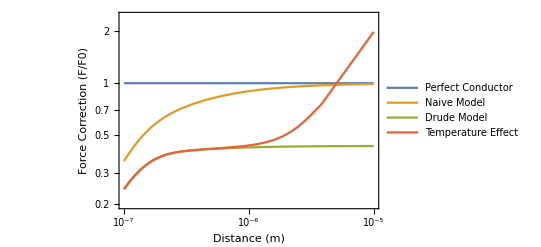

```mathematica
LogLogPlot[{1,Fcorrected[1,L,radius,0]/Fperfect[L,radius],Fcorrected[2,L,radius,0]/Fperfect[L,radius],Fcorrected[2,L,radius,300]/Fperfect[L,radius]},{L,1.0*^-7,1*^-5},Frame->True,PlotRangePadding->{None,0.1},PlotRange->{{1.*^-7,1*^-5},Full},FrameLabel->{"Distance (m)","Force Correction (F/F0)"},ImageSize->Scaled[0.8],PlotLegends->{"Perfect Conductor","Naive Model","Drude Model","Temperature Effect"}]
```

```mathematica
Fperfect[1*^-6,5*^6]
Table[Fperfect[L,0.113]*TempCorrection[300,L],{L,5*^-7,1*^-5,0.000001}]
```

0.0135558

{2.45989×10^-9,9.83095×10^-11,2.56737×10^-11,1.17428×10^-11,6.94533×10^-12,4.64937×10^-12,3.32885×10^-12,2.50034×10^-12,1.94664×10^-12,1.55839×10^-12}

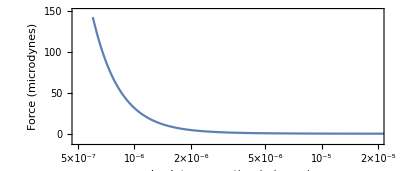

```mathematica
LogLinearPlot[Fperfect[L,0.113]*TempCorrection[300,L]/1*^-11,{L,6*^-7,10*^-5},PlotRange->{{0.5*^-6,20*^-6},{-10,150}},AspectRatio->3/7,Frame->True,FrameLabel->{"absolute separation (microns)","Force (microdynes)"},ImageSize->Scaled[0.8]]
```

```mathematica
vals=Import["/Users/noah/Desktop/byL.txt",TSV]
```

Import::noelem: The Import element "TSV" is not present when importing as "Text".

$Failed

```mathematica
vals
```

1.58489 -6.590162e-03 3.900835e-05 -8.550697e-03 2.905062e-05 
10.0 -3.619472e-05 2.059170e-07 -1.301092e-05 3.389436e-08 
2.51189 -2.348352e-03 9.562701e-06 -2.270734e-03 6.402078e-06 
3.16228 -1.313436e-03 4.911075e-06 -1.089207e-03 2.678927e-06 
3.98107 -7.018182e-04 5.232377e-06 -4.973771e-04 1.532404e-06 
5.01187 -3.580661e-04 2.156643e-06 -2.160983e-04 4.683816e-07 
6.30957 -1.743648e-04 8.637860e-07 -8.913758e-05 1.380527e-07 
7.94328 -8.116374e-05 3.444017e-07 -3.491819e-05 5.414972e-08

```mathematica
vals[[1]]
```

Part::partd: Part specification "1.58489 -6.590162e-03 3.900835e-05 -8.550697e-03 2.905062e-05 \n10.0 -3.619472e-05 2.059170e-07 -1.301092e-05 3.389436e-08 \n2.51189 -2.348352e-03 9.562701e-06 -2.270734e-03 6.40207" … "-3.580661e-04 2.156643e-06 -2.160983e-04 4.683816e-07 \n6.30957 -1.743648e-04 8.637860e-07 -8.913758e-05 1.380527e-07 \n7.94328 -8.116374e-05 3.444017e-07 -3.491819e-05 5.414972e-08 " ⟦ 1 ⟧ is longer than depth of object.

1.58489 -6.590162e-03 3.900835e-05 -8.550697e-03 2.905062e-05 
10.0 -3.619472e-05 2.059170e-07 -1.301092e-05 3.389436e-08 
2.51189 -2.348352e-03 9.562701e-06 -2.270734e-03 6.402078e-06 
3.16228 -1.313436e-03 4.911075e-06 -1.089207e-03 2.678927e-06 
3.98107 -7.018182e-04 5.232377e-06 -4.973771e-04 1.532404e-06 
5.01187 -3.580661e-04 2.156643e-06 -2.160983e-04 4.683816e-07 
6.30957 -1.743648e-04 8.637860e-07 -8.913758e-05 1.380527e-07 
7.94328 -8.116374e-05 3.444017e-07 -3.491819e-05 5.414972e-08 ⟦1⟧